```mathematica
<<C:\Users\jeoku\OneDrive\Documents\chapman\CS533\programs\ARlags.m;
```

```mathematica
<<C:\Users\jeoku\OneDrive\Documents\chapman\CS533\data\BRLpCADpGBPpJPYpMXNpNOKpTRLpUSD.txt;
```

```mathematica
Off[General::munfl]
```

```mathematica
(*  We can apply our estimation fucntions to exchange rates.  We   *)
(*  start with many lags and pare away the ones with p-values      *)
(*  that are below 0.05.                                           *)
```

```mathematica
(*  CAD per USD                                                    *)
```

```mathematica
LagTestn[Transpose[CADpUSD][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0108513 | 0.00588056 | 1.84528 | 0.0655078
a | 0.00894579 | 0.00498432 | 1.79479 | 0.0732093
b1 | 0.245603 | 0.0414907 | 5.91947 | 5.53526×10^-9
b2 | -0.0210307 | 0.0427245 | -0.492239 | 0.622737
b3 | -0.0686429 | 0.0426426 | -1.60973 | 0.108003
b4 | 0.0865324 | 0.042727 | 2.02524 | 0.043301
b5 | 0.0137284 | 0.0429258 | 0.319816 | 0.749223
b6 | 0.0263025 | 0.0428557 | 0.613745 | 0.539625
b7 | -0.0475151 | 0.0429854 | -1.10538 | 0.269456
b8 | -0.0106296 | 0.04301 | -0.247142 | 0.804886
b9 | -0.0101445 | 0.0418853 | -0.242198 | 0.808712,0.0748788,1.20845}

```mathematica
LagTestn[Transpose[CADpUSD][[2]],1]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0110532 | 0.00568744 | 1.94344 | 0.052434
a | 0.00916526 | 0.0048163 | 1.90297 | 0.0575272
b1 | 0.235357 | 0.039897 | 5.89912 | 6.13401×10^-9,0.0587992,1.20473}

```mathematica
(*  USD per GBP                                                    *)
```

```mathematica
LagTestn[Transpose[USDpGBP][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0343875 | 0.0108001 | 3.18399 | 0.00153062
a | 0.0244107 | 0.0076789 | 3.17893 | 0.00155709
b1 | 0.335074 | 0.0412795 | 8.1172 | 2.87728×10^-15
b2 | -0.0787701 | 0.0435551 | -1.80852 | 0.0710448
b3 | 0.089532 | 0.0435484 | 2.05592 | 0.0402379
b4 | 0.0161592 | 0.0437297 | 0.369524 | 0.711872
b5 | -0.0476217 | 0.0437074 | -1.08956 | 0.276361
b6 | 0.0383645 | 0.0437506 | 0.87689 | 0.38091
b7 | -0.061267 | 0.0436811 | -1.40259 | 0.161274
b8 | 0.0188534 | 0.043572 | 0.432695 | 0.665397
b9 | 0.0341027 | 0.0415461 | 0.82084 | 0.412075,0.122562,1.4079}

```mathematica
LagTestn[Transpose[USDpGBP][[2]],1]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0334394 | 0.0100037 | 3.34272 | 0.000881701
a | 0.0237371 | 0.00711901 | 3.33433 | 0.00090822
b1 | 0.310774 | 0.0388783 | 7.9935 | 6.84563×10^-15,0.107054,1.40882}

```mathematica
(*  JPY per USD                                                    *)
```

```mathematica
LagTestn[Transpose[JPYpUSD][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.51211 | 0.493554 | 3.06372 | 0.0022877
a | 0.0161582 | 0.00496857 | 3.25209 | 0.00121223
b1 | 0.310125 | 0.0411491 | 7.5366 | 1.86923×10^-13
b2 | -0.0415719 | 0.0422062 | -0.984972 | 0.325049
b3 | 0.034841 | 0.0421327 | 0.826934 | 0.408615
b4 | 0.0252684 | 0.0420648 | 0.600703 | 0.548273
b5 | -0.0240922 | 0.0420667 | -0.572713 | 0.567061
b6 | -0.0657955 | 0.0420682 | -1.56402 | 0.11836
b7 | 0.0443302 | 0.0421264 | 1.05231 | 0.293094
b8 | -0.00452629 | 0.0421307 | -0.107435 | 0.914481
b9 | 0.0423765 | 0.040222 | 1.05357 | 0.292521,0.117206,93.565}

```mathematica
LagTestn[Transpose[JPYpUSD][[2]],1]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.57923 | 0.460449 | 3.42977 | 0.000645915
a | 0.0169098 | 0.00457203 | 3.69853 | 0.000236931
b1 | 0.294701 | 0.0386932 | 7.61635 | 1.03144×10^-13,0.110215,93.4254}

```mathematica
(*  NOK per USD                                                    *)
```

```mathematica
LagTestn[Transpose[NOKpUSD][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0951406 | 0.0456232 | 2.08536 | 0.0374743
a | 0.0134766 | 0.00656447 | 2.05297 | 0.0405244
b1 | 0.330736 | 0.0414867 | 7.97209 | 8.35226×10^-15
b2 | -0.0723798 | 0.043707 | -1.65602 | 0.0982593
b3 | -0.0169135 | 0.0437826 | -0.386305 | 0.699413
b4 | 0.0135577 | 0.0438209 | 0.30939 | 0.757136
b5 | 0.020152 | 0.0439966 | 0.458035 | 0.647099
b6 | 0.0577616 | 0.0440089 | 1.3125 | 0.189873
b7 | -0.00807194 | 0.0442573 | -0.182386 | 0.855343
b8 | 0.0210321 | 0.04421 | 0.475732 | 0.634445
b9 | -0.0749435 | 0.0424484 | -1.76552 | 0.078003,0.114782,7.03165}

```mathematica
LagTestn[Transpose[NOKpUSD][[2]],1]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.103999 | 0.0426571 | 2.43801 | 0.0150599
a | 0.0148473 | 0.00610753 | 2.43098 | 0.0153524
b1 | 0.311758 | 0.039275 | 7.93781 | 1.02837×10^-14,0.0995122,7.00491}

```mathematica
(*  JPY per GBP                                                    *)
```

```mathematica
LagTestn[Transpose[JPYpGBP][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.92471 | 0.858741 | 3.40581 | 0.000705382
a | 0.021928 | 0.00627702 | 3.49338 | 0.000513378
b1 | 0.288801 | 0.0409221 | 7.05734 | 4.87078×10^-12
b2 | 0.0123292 | 0.0423606 | 0.291054 | 0.771115
b3 | 0.0875205 | 0.0423522 | 2.06649 | 0.0392263
b4 | -0.0195244 | 0.0424908 | -0.459497 | 0.64605
b5 | 0.0167341 | 0.0425403 | 0.393372 | 0.69419
b6 | -0.0369143 | 0.0425148 | -0.868271 | 0.385606
b7 | 0.00417298 | 0.0424677 | 0.0982624 | 0.921758
b8 | 0.0367752 | 0.0424981 | 0.865339 | 0.387211
b9 | 0.120336 | 0.0409757 | 2.93675 | 0.00344851,0.126697,133.836}

```mathematica
(*  Notice that the significant lags for the yen to pound        *)
(*  exchange rate are not consecutive.  In order to select       *)
(*  only the lags that are significant we need to have an        *)
(*  indicator function on the lags that are significant.         *)
(*  This is a fucntion with a different name (LagTest            *)
(*  rather than LagTestn).  Also the second argument is          *)
(*  a vector of indicator functions rather than an integer.      *)
```

```mathematica
LagTest[Transpose[JPYpGBP][[2]], {1, 0, 1, 0, 0,0,0,0,1}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.80575 | 0.811832 | 3.45608 | 0.000587225
a | 0.0209681 | 0.0058921 | 3.55868 | 0.000402492
b1 | 0.289428 | 0.0387436 | 7.47035 | 2.87247×10^-13
b3 | 0.0838046 | 0.0389465 | 2.15179 | 0.0318166
b9 | 0.127419 | 0.0389488 | 3.27144 | 0.001132,0.122936,133.81}

```mathematica
(*  This is one of our familiar simulations with a positive      *)
(*  adjustment rate.                                             *)
```

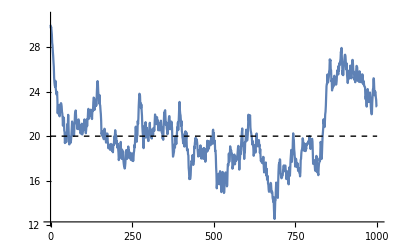

```mathematica
PriceSequenceGraphLags[{0, 0, 0, 0, 0, 0, 0, 0, 0},0.02,30,20,1000,0.5, True]
```

```mathematica
(*  This adjustment is similar to the previous one with one modification:       *)
(*  it has a single lag with coefficient 1 on the term (p_{t-1} - p_{t - 2}).  *)
```

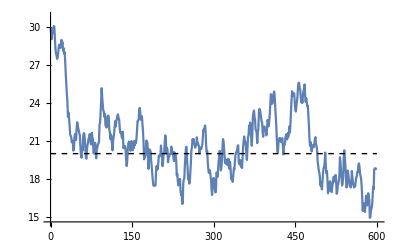

```mathematica
PriceSequenceGraphLags[{0.3, 0, 0, 0, 0, 0, 0, 0, 0},0.02,30,20,600,0.5,True]
```

```mathematica
(*  The next function creates a sequence that we will estimate   *)
(*  with different lags.                                         *)
```

```mathematica
c02n600Lag158 = PriceSequenceLags[{0.55, 0, 0, 0, 0.3, 0, 0, 0.1, 0},0.02,18,20,600,1];
```

```mathematica
LagTestn[Transpose[c02n600Lag158][[2]],9]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.441148 | 0.0774128 | 5.69864 | 1.92447×10^-8
a | 0.020663 | 0.00305373 | 6.76649 | 3.23813×10^-11
b1 | 0.488172 | 0.040813 | 11.9612 | 1.27558×10^-29
b2 | -0.0161067 | 0.0453251 | -0.35536 | 0.722449
b3 | -0.0276955 | 0.045443 | -0.609455 | 0.542462
b4 | 0.0191996 | 0.045463 | 0.422311 | 0.672955
b5 | 0.34714 | 0.0434716 | 7.98545 | 7.57632×10^-15
b6 | -0.0132505 | 0.0458036 | -0.28929 | 0.772463
b7 | 0.0257725 | 0.0457705 | 0.563082 | 0.573597
b8 | 0.14456 | 0.0458955 | 3.14977 | 0.00171827
b9 | -0.01341 | 0.0419849 | -0.3194 | 0.749538,0.598228,21.7272}

```mathematica
LagTestn[Transpose[c02n600Lag158][[2]],8]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.447059 | 0.0750236 | 5.95891 | 4.40433×10^-9
a | 0.0209436 | 0.00291993 | 7.17264 | 2.24988×10^-12
b1 | 0.486677 | 0.040476 | 12.0238 | 6.79734×10^-30
b2 | -0.0161758 | 0.0452216 | -0.3577 | 0.720698
b3 | -0.0273729 | 0.0453034 | -0.604213 | 0.545938
b4 | 0.0149737 | 0.0433941 | 0.345064 | 0.730171
b5 | 0.34721 | 0.0434 | 8.00024 | 6.76317×10^-15
b6 | -0.0125952 | 0.0456827 | -0.275712 | 0.782868
b7 | 0.0261987 | 0.0456688 | 0.573668 | 0.566415
b8 | 0.138271 | 0.0413828 | 3.34128 | 0.000887481,0.598412,21.7224}

```mathematica
LagTest[Transpose[c02n600Lag158][[2]],{1, 0, 0, 0, 1, 0, 0, 1, 0}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.446537 | 0.0733505 | 6.08772 | 2.05578×10^-9
a | 0.0205587 | 0.00283497 | 7.25181 | 1.28786×10^-12
b1 | 0.47813 | 0.0318089 | 15.0313 | 1.63676×10^-43
b5 | 0.345794 | 0.0317184 | 10.902 | 2.36454×10^-25
b8 | 0.135469 | 0.0335887 | 4.03319 | 0.000062203,0.597416,21.7201}

```mathematica
(*  We have exchange rates for yen per U.S. dollar and for U.S.     *)
(*  dollars per British pound.  If we multiply those two rates      *)
(*  together we get a rate that has the same dimensions as the      *)
(*  exchange rate between the yen and the pound: ¥/$ * $/£ = ¥/£.  *)
(*  The important question is whether the rate from the product     *)(*  of the yen per dollar series and the dollar per pound series    *)
(*  is the same as the yen per pounnd series.                       *)
```

```mathematica
JPYpUSDxUSDpGBP = N[Transpose[{Transpose[CADpUSD][[1]], Table[Transpose[JPYpUSD][[2]][[i]] * Transpose[USDpGBP][[2]][[i]], {i, 1, Length[JPYpUSD]}]}]];
```

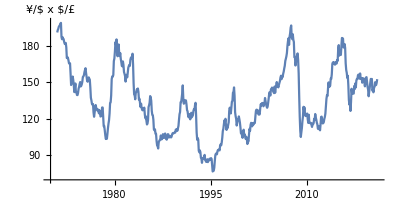

```mathematica
ListPlot[JPYpUSDxUSDpGBP, PlotRange -> {{1970, 2021}, {70, 200}}, Joined -> True, AxesOrigin -> {1970, 70}, AxesLabel -> {"", "¥/$ x $/£"}, AspectRatio -> 0.5]
```

```mathematica
JPYpUSDxUSDpGBPoverJPYpGBP = N[Transpose[{Transpose[CADpUSD][[1]], Table[Transpose[JPYpUSD][[2]][[i]] * Transpose[USDpGBP][[2]][[i]]/Transpose[JPYpGBP][[2]][[i]], {i, 1, Length[JPYpUSD]}]}]];
```

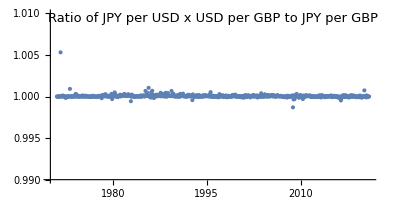

```mathematica
Show[ListPlot[JPYpUSDxUSDpGBPoverJPYpGBP, PlotRange -> {{1970, 2021}, {0.99, 1.01}}, AxesOrigin -> {1970,0.99}, AspectRatio -> 0.5],Graphics[Text[StyleForm["Ratio of JPY per USD x USD per GBP to JPY per GBP", FontSlant -> Plain, 
                               FontFamily -> "TimesNewRoman", 13], 
                               {1996, 1.0094}]]]
```

```mathematica
Sort[Transpose[JPYpUSDxUSDpGBPoverJPYpGBP ][[2]]];
```

```mathematica
(*  For the purposes of estimating the adjustment rates we should    *)
(*  be able to use the product series as a way to get additional     *)
(*  real exchange rate series.                                       *)
(*  The series CADpGBP can be constructed from CADpUSD and USDpGBP.  *)
```

```mathematica
(*  Another series is JPYpNOK.  Find this series from JPYpUSD    *)
(*  and NOKpUSD.  Hint: Use the reciprocal of NOKpUSD as the     *)
(*  rate for USDpNOK in the formula for multiplying the series   *)
(*  together.  If you have done that correctly your series for   *)
(*  JPYpNOK should look like the next graph.                     *)
```

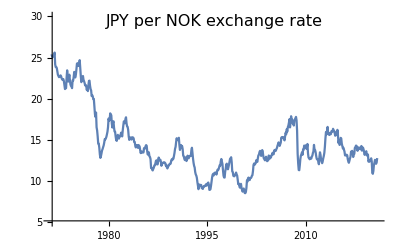

```mathematica
(*                       HOMEWORK PROBLEM 5                       *)
```

```mathematica
(*  FILL OUT TWO NEW ROWS WITH THE SAME ENTRIES THAT WE HAVE IN   *)
(*  TABLE 6 IN THE LECTURE NOTES, ADDING IN ROWS FOR CADpGBP AND  *)
(*  JPYpNOK.                                                      *)
```

```mathematica
(*                       Francis: Replicating results  Table 6:page 36 of lecture notes                    *)
```

```mathematica
JPYpUSDxUSDpGBP = N[Transpose[{Transpose[CADpUSD][[1]], Table[Transpose[JPYpUSD][[2]][[i]] * Transpose[USDpGBP][[2]][[i]], {i, 1, Length[JPYpUSD]}]}]];
```

```mathematica
LagTest[Transpose[JPYpUSDxUSDpGBP][[2]],{1, 0, 1, 0, 0, 0, 0, 0, 1}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 2.814 | 0.813235 | 3.46025 | 0.000578378
a | 0.0210279 | 0.00590196 | 3.56288 | 0.000396249
b1 | 0.287397 | 0.0387568 | 7.4154 | 4.20299×10^-13
b3 | 0.0846831 | 0.0389598 | 2.1736 | 0.0301293
b9 | 0.128725 | 0.0389619 | 3.30386 | 0.00101098,0.122191,133.822}

```mathematica
(*                       Francis: reproducing for Canadian Dollar -HW#5                     *)
```

```mathematica
CADpUSDxUSDpGBP = N[Transpose[{Transpose[CADpUSD][[1]], Table[Transpose[CADpUSD][[2]][[i]] * Transpose[USDpGBP][[2]][[i]], {i, 1, Length[CADpUSD]}]}]];
```

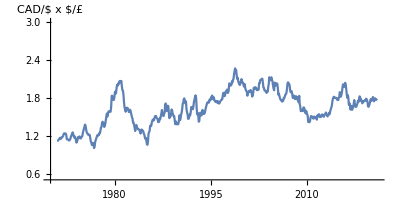

```mathematica
ListPlot[CADpUSDxUSDpGBP, PlotRange -> {{1970, 2021}, {0.5, 3}}, Joined -> True, AxesOrigin -> {1970, 0.5}, AxesLabel -> {"", "CAD/$ x $/£"}, AspectRatio -> 0.5]
```

```mathematica
LagTest[Transpose[CADpUSDxUSDpGBP][[2]],{1, 0, 0, 0, 0, 0, 0, 0, 0}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0247034 | 0.00935725 | 2.64003 | 0.00850691
a | 0.0146322 | 0.00565848 | 2.58589 | 0.00994894
b1 | 0.240567 | 0.0396484 | 6.06752 | 2.31024×10^-9,0.0657749,1.68829}

```mathematica
(*                       Francis: reproducing for Norvegenian Kroner -HW#6 Note: reciprocal of NOK/USD was multiplied              *)
```

```mathematica
JPYpNOK = N[Transpose[{Transpose[CADpUSD][[1]], Table[Transpose[JPYpUSD][[2]][[i]] * Transpose[1/NOKpUSD][[2]][[i]], {i, 1, Length[CADpUSD]}]}]];
```

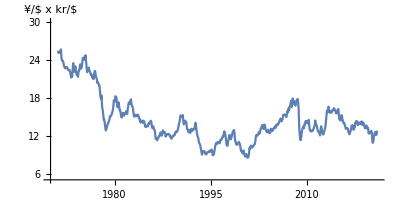

```mathematica
ListPlot[JPYpNOK, PlotRange -> {{1970, 2021}, {5, 30}}, Joined -> True, AxesOrigin -> {1970, 5}, AxesLabel -> {"", "¥/$ x kr/$"}, AspectRatio -> 0.5]
```

```mathematica
LagTest[Transpose[JPYpNOK ][[2]],{1, 0, 0, 0, 0, 0, 0, 0, 0}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.163532 | 0.0636801 | 2.56803 | 0.0104705
a | 0.0122763 | 0.00424316 | 2.89319 | 0.00395287
b1 | 0.279788 | 0.0391112 | 7.15366 | 2.48867×10^-12,0.0910785,13.321}